# ME 8381 Bioheat Mass Transfer Project 1 - Nanoparticle heating for cancer treatment - FeO NPs

## 1. Definitions and Tissue/Tumor Properties

```mathematica
ktherm=0.461; (* W/m-K *)
ρt=1045;(* kg/m^3*)
ct=3600; (* J/kg-K *)
α=ktherm/(ρt ct); (* m^2/s *)

(* Properties *)
rtumor=0.01;
rtissue=0.10;
ρb=1058; (* kg/m^3*)
cb=3840; (* J/kg-K *)

a=3;(*for spherical coordinates*)
timetreat=60*60; (* 60 Minute Treatment Time *)
```

## 2. SAR of FeO Nanoparticle

### 2.1 Magnetic Relaxation Heating and SAR

```mathematica
(* FUNDAMENTAL CONSTANTS *)
Kb =1.381*^-23; (* Boltzman Constant [(m^2 kg)/(s^2 K)] *)
μo=4π 1*^-7; (* Permeability of Free Space [N/A^2] *)


(* NANOPARTICLE PROPERTIES *)
dfeo=12.5*^-9; (* Average Diameter of Nanoparticles [ m ] *)
σfeo=0.25; (* Standard Deviation of Nanoparticle Diameter *)
δfeo=2*^-9; (* Thickness of Surface Coating [ m ] *)

Ka=23000; (* Magnetic Anisotropy Constant [ J/m^3 ] *)
Md=446000; (* Domain Magnetization [ A/m ] *)
τo=10^-9; (* Attempt Time [ s ] *)

ρfeo=5180; (* Density of Bulk Magnetic Material [ kg/m^3 ] *) 
cfeo=670; (* Specific Heat of Bulk Magnetic Material [ j/(kg K) ] *)

rfeo=dfeo/2; (* Average Radius of Nanoparticle [ m ] *)


(* MATRIX FLUID PARAMETERS *)
Tfluid=273.15+37.6; (* Ambient Temperature [ K ] *)
η=0.000678; (* Dynamic Viscosity of Fluid [ kg/(m s) ] *)
ρfluid=999; (* Density of Fluid [ kg/m^3 ] *)
cfluid=4180; (* Specific Heat of Fluid [ j/(kg K) ] *)

ϕo=0.005; (* Volume Fraction of Solids [ (m^3 nanoparticles)/(m^3 (solute or tissue)) ] *)


(* MAGNETIC FIELD PARAMETERS *)
f=100000; (* Frequency [ Hz ] *)
(* Subscript[B, 0]=0.09; Magnetic Induction [ T ] *)
Ho= 5000 ; (* Magnetic Field Strength [ A/m ] *)


(* NUMERICAL INTEGRATION FOR POLYDISPERSIVE POWER *)

nINT = 1000; (* Discretization for Numerical Integration [ NA ] *)

rmin=rfeo ( 1 - 3 σfeo ); (* Minimum Radius for Numerical Integration [ m ] *)
rmax=rfeo ( 1 + 3 σfeo ); (* Maximum Radius for Numerical Integration [ m ] *)
Δr=(rmax-rmin)/nINT; (* Increment for Numerical Integration [ m ] *)
ro=rfeo/Exp[ σfeo^2/2]; (* Median Radius for Log Normal Distribution [ m ] *)

(* Ensure Radius Integration Range is Positive *)
If[ rmin<0,rmin=0,rmin=rmin];

rint=rmin+Δr/2; (* Initial Radius for Numerical Integration *)
Pfeo=0; (* Initialize Power for Numerical Integration *)

(* NUMERICAL INTEGRATION OF POLYDISPERSE PARTICLE POWER GENERATION *)
For[ i =1 , i ≤ nINT , i++,

	Vm=(4π rint^3)/3; (* Magnetic NP Volume [ m^3 ] *)
	Vh=(1+δfeo/rint)^3 Vm; (* Hydrodynamic NP Volume [ m^3 ] *)
	τB=(3 η Vh)/(Kb Tfluid); (* Brownian Relaxation Time [ s ] *)
	Γ=(Ka Vm)/(Kb Tfluid); (* Gamma Numerical Constant [ NA ] *)
	τN=(√π)/2 τo Exp[Γ]/(√Γ); (* Neel Relaxation Time [ s ] *)
	τtotal=(τN τB)/(τN+τB); (* Effective Relaxation Time [ s ] *)
	ζ=(μo Md Ho Vm)/(Kb Tfluid); (* Langevin Function [ NA ] *)
	χo=(ϕo μo Md^2 Vm)/(Kb Tfluid ζ)(Coth[ζ]-1/ζ); (* Actual Magnetic Susceptibility [ NA ] *)
	Pint=π μo χo f Ho^2 (2 π f τtotal)/(1 + (2 π f τtotal)^2); (* Discrete Volumetric Power Generation [ W/m^3 ] *)

	gint=1/(√(2 π) σfeo rint) Exp[ -Log[ rint/ro]^2/(2 σfeo^2)]; (* Log Normal Distribution Function [ NA ] *)

	Pfeo=Pfeo +Pint gint Δr; (* Numerical Sum of Volumetric Power Generation [ W/m^3 ] *)

	rint=rint+Δr; (* Increment Numerical Integration Radius *) ]

SARfeo[ NV_ ] := Pfeo NV (4/3 π rfeo^3)/ϕo; (* SAR Will Vary Linearly with Concentration [ W / m^3 ] *)
```

### 2.2 FeO Concentration

```mathematica
(*Varying FeO concentration*)
ntumor=0.10; (* Normalized NP Concentration at Edge of Tumor *)
aa=Log[1/ntumor]; (* Fit Constant for Exponential NP Distribution *)
nfeo=24 (* Injections *) 0.5 (* ml per injection *) 120 (* Ferrofluid Concentration [(mg Fe)/ml] *) 1/55.84 (* 1/(molecular weight Fe) [(mol Fe)/(g Fe)] *) 1/1000 (* (g Fe)/(mg Fe) *) 1/3 (* (mol Subscript[Fe, 3] Subscript[O, 4])/(mol Fe) *) 231.54 (* molecular weight magnetite [(g Subscript[Fe, 3] Subscript[O, 4])/(mol Subscript[Fe, 3] Subscript[O, 4])] *) 1/5180 (* 1/(density magnetite) [m^3/(kg Subscript[Fe, 3] Subscript[O, 4])] *) 1/1000 (* (kg Subscript[Fe, 3] Subscript[O, 4])/(g Subscript[Fe, 3] Subscript[O, 4]) *) 1/(4/3 π rfeo^3) (* 1/(volume of Subscript[Fe, 3] Subscript[O, 4] NP) *);  (* Number of FeO at the Treatment Site *)
nfeo=1 10^16;
CONSfeo=nfeo/(4/3 π rtumor^3); (* Constant Nanoparticle Concentration in Tumor [ 1/m^3 ] *)
NCONfeo[x_]:=If[x ≤ rtumor,CONSfeo,0]
Afeo=nfeo/Integrate[ 4 π R^2 Exp[ -aa R/rtumor], {R,0,rtissue}]; (* Subscript[A, FeO] is a Constant for Calculating Exponential FeO NP Distribution *)
NEXPfeo[ R_ ]:=Afeo Exp[ -aa R/rtumor]; (* Radius Dependant FeO NP Exponential Concentration Distribution *)

Plot[ NEXPfeo[ x ] , {x,0, rtissue},PlotRange->All,AxesLabel->{Radius [m],NP Concentration [m^-3]}]
```

-Graphics-

```mathematica
SARfeo[NCONfeo[0.005]]
```

125139.

## 3. Heat Transfer Calculation

### 3.1 Effect of Blood Perfusion (with and without perfusion for constant concentration and field intensity)

-Graphics3D-

-Graphics3D-

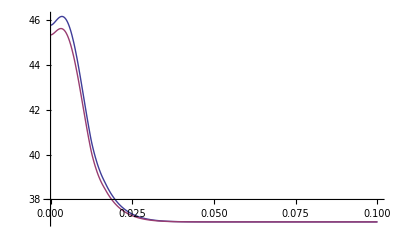

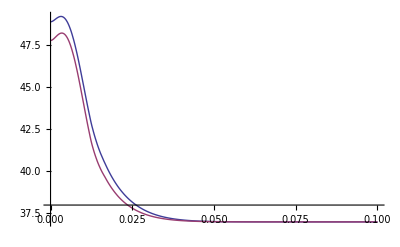

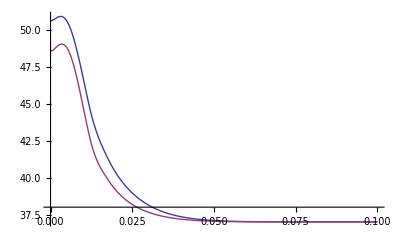

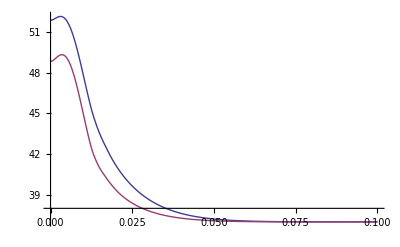

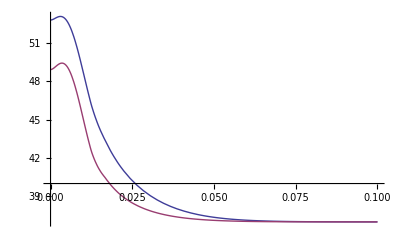

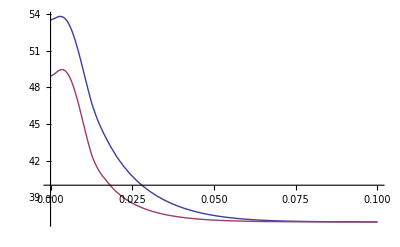

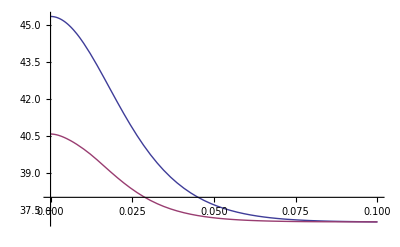

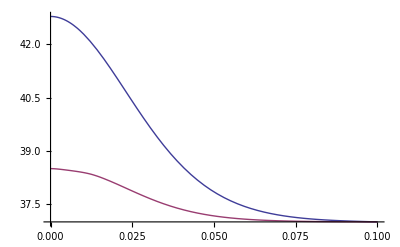

```mathematica
solutionNoPer=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeo[x]],0],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
solutionPer=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeo[x]],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumor,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
Plot3D[Evaluate[u[x,t]/.First[solutionNoPer]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]
Plot3D[Evaluate[u[x,t]/.First[solutionPer]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionNoPer]],Evaluate[u[x,t]/.First[solutionPer]]},{x,10^-20,rtissue},PlotRange->All]],{t,600,timetreat*2,600}]
```

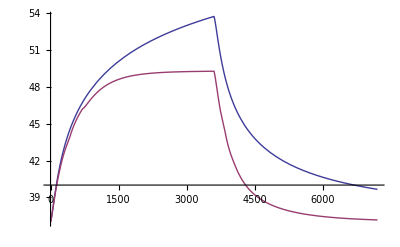

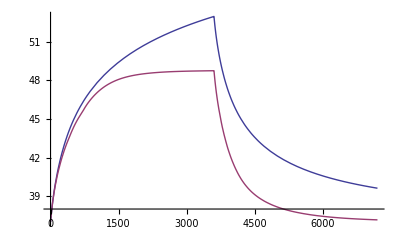

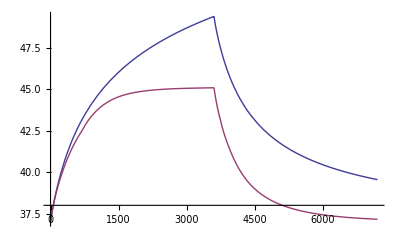

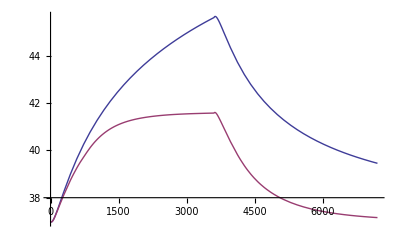

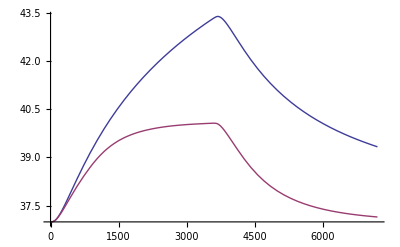

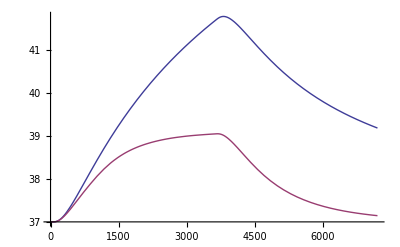

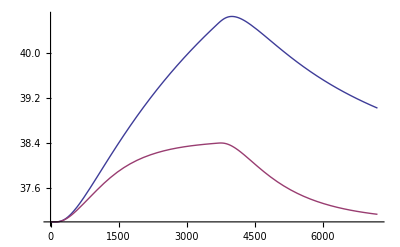

```mathematica
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionNoPer]],Evaluate[u[x,t]/.First[solutionPer]]},{t,0,timetreat*2},PlotRange->All]],{x,0.002,0.026,0.004}]
```

### 3.2 Effect of Nanoparticle Concentraiton (0.1, 0.5, 1, 2 times CONfeo)

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

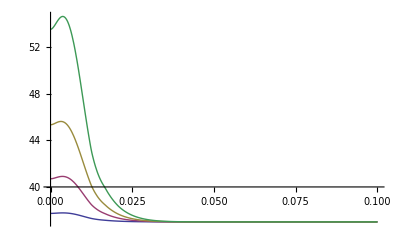

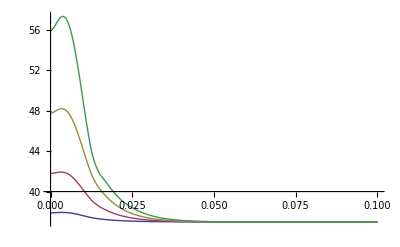

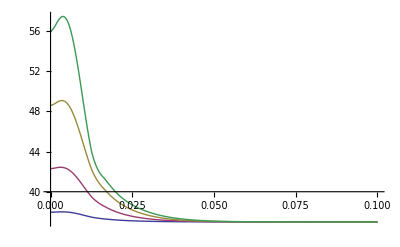

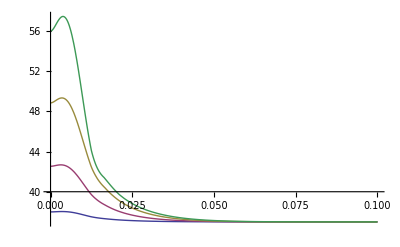

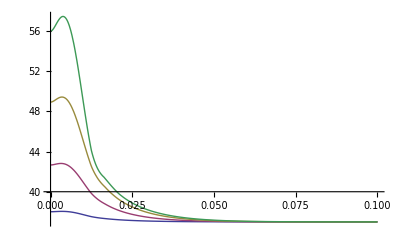

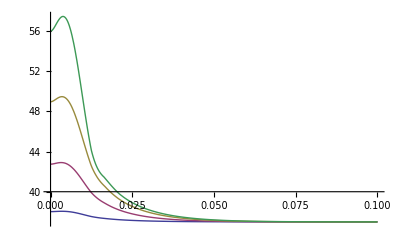

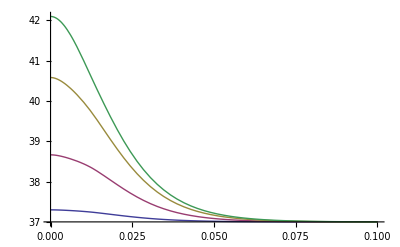

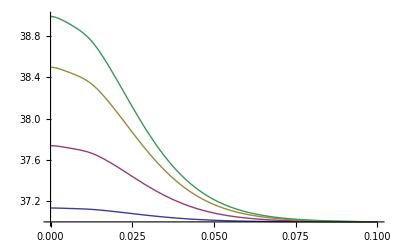

```mathematica
solutionCONfeo10P=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeo[x]*0.1],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumor,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
Plot3D[Evaluate[u[x,t]/.First[solutionCONfeo10P]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]

solutionCONfeo50P=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeo[x]*0.5],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumor,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
Plot3D[Evaluate[u[x,t]/.First[solutionCONfeo50P]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]

solutionCONfeo=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeo[x]],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumor,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
Plot3D[Evaluate[u[x,t]/.First[solutionCONfeo]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]

solutionCONfeo2T=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeo[x]*2],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumor,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
Plot3D[Evaluate[u[x,t]/.First[solutionCONfeo2T]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]

Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionCONfeo10P]],Evaluate[u[x,t]/.First[solutionCONfeo50P]],Evaluate[u[x,t]/.First[solutionCONfeo]],Evaluate[u[x,t]/.First[solutionCONfeo2T]]},{x,10^-20,rtissue},PlotRange->All]],{t,600,timetreat*2,600}]
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionCONfeo10P]],Evaluate[u[x,t]/.First[solutionCONfeo50P]],Evaluate[u[x,t]/.First[solutionCONfeo]],Evaluate[u[x,t]/.First[solutionCONfeo2T]]},{t,0,timetreat*2},PlotRange->All]],{x,0.002,0.026,0.004}]
```

### 3.3 Effect of FeO biodistribution (Uniform vs. Nonuniform)

#### Uniform FeO concentration (FeO)

```mathematica
solutionCONfeo=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeo[x]],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumor,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
Plot3D[Evaluate[u[x,t]/.First[solutionCONfeo]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]
```

-Graphics3D-

#### Exponentially changing FeO concentration

```mathematica
solutionEXPfeo=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NEXPfeo[x]],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumor,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];

Plot3D[Evaluate[u[x,t]/.First[solutionEXPfeo]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]
```

-Graphics3D-

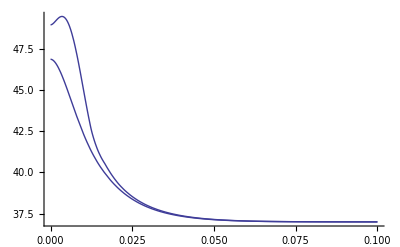

```mathematica
PlotCON=Plot[Evaluate[u[x,t]/.solutionCONfeo/.t->3600],{x,10^-20,rtissue},PlotRange->All,AxesOrigin->{0,36}];
PlotEXP=Plot[Evaluate[u[x,t]/.solutionEXPfeo/.t->3600],{x,10^-20,rtissue},PlotRange->All];
Show[PlotCON,PlotEXP]
```

#### Compare : Constant FeO distribution vs. Exponentially distributing FeO

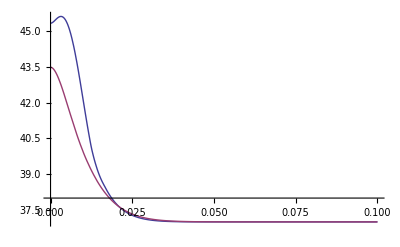

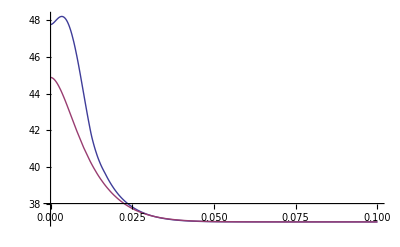

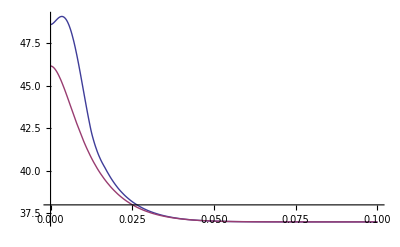

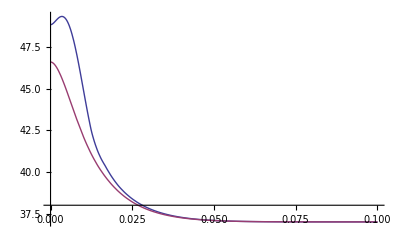

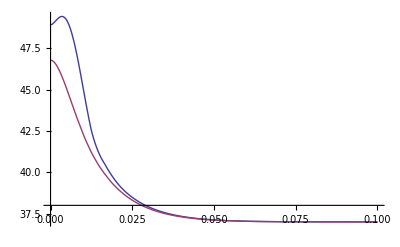

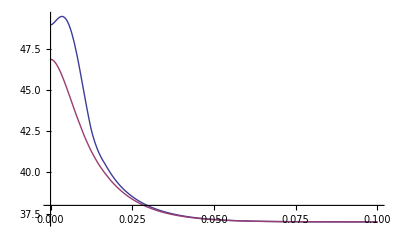

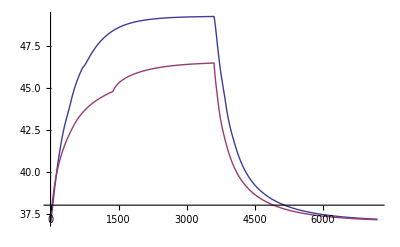

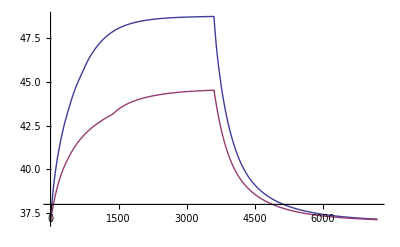

```mathematica
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionCONfeo]],Evaluate[u[x,t]/.First[solutionEXPfeo]]},{x,10^-20,rtissue},PlotRange->All]],{t,600,timetreat,600}]
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionCONfeo]],Evaluate[u[x,t]/.First[solutionEXPfeo]]},{t,0,timetreat*2},PlotRange->All]],{x,0.002,0.026,0.004}]
```

#### 3.1 .5 Treatable tumor size (Radius: 0.1cm - S1, 0.5cm - S2, 1cm - S3, 2cm - S4)

```mathematica
rtumorS1=.001;
rtumorS2=.005;
rtumorS3=.01;
rtumorS4=.02;
NCONfeoS1[x_]:=If[x ≤ rtumorS1,CONSfeo,0]
NCONfeoS2[x_]:=If[x ≤ rtumorS2,CONSfeo,0]
NCONfeoS3[x_]:=If[x ≤ rtumorS3,CONSfeo,0]
NCONfeoS4[x_]:=If[x ≤ rtumorS4,CONSfeo,0]

solutionS1=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeoS1[x]],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumorS1,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
Plot3D[Evaluate[u[x,t]/.First[solutionS2]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]

solutionS2=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeoS2[x]],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumorS2,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
Plot3D[Evaluate[u[x,t]/.First[solutionS2]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]

solutionS3=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeoS3[x]],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumorS3,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
Plot3D[Evaluate[u[x,t]/.First[solutionS3]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]

solutionS4=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeoS4[x]],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumorS4,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*2}];
Plot3D[Evaluate[u[x,t]/.First[solutionS4]],{x,10^-20,rtissue},{t,0,timetreat*2},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

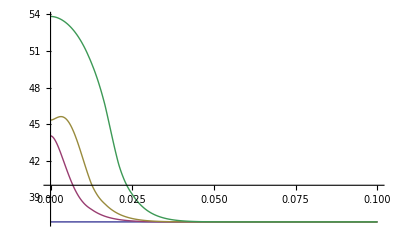

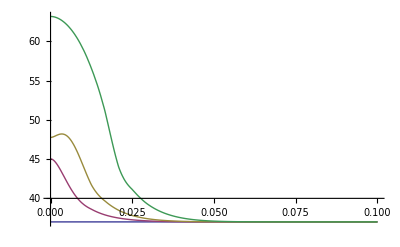

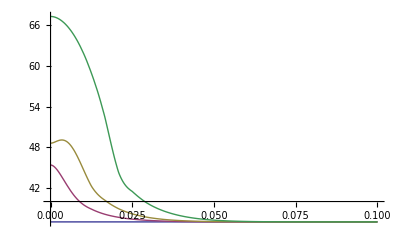

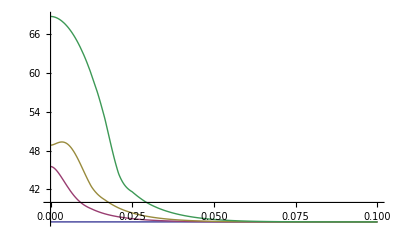

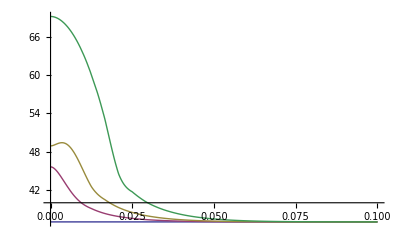

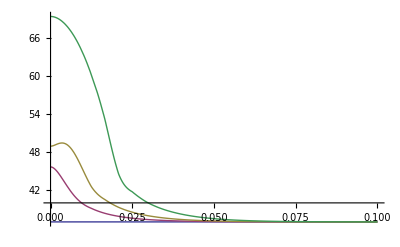

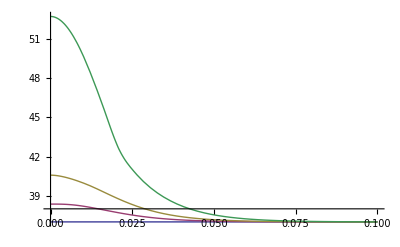

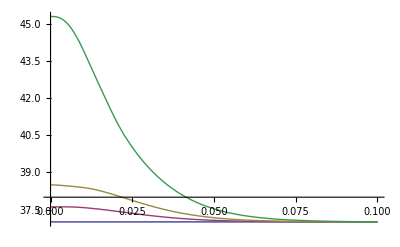

```mathematica
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionS1]],Evaluate[u[x,t]/.First[solutionS2]],Evaluate[u[x,t]/.First[solutionS3]],Evaluate[u[x,t]/.First[solutionS4]]},{x,10^-20,rtissue},PlotRange->All]],{t,600,timetreat*2,600}]
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionS1]],Evaluate[u[x,t]/.First[solutionS2]],Evaluate[u[x,t]/.First[solutionS3]],Evaluate[u[x,t]/.First[solutionS4]]},{t,0,timetreat*2},PlotRange->All]],{x,10^-20,10^-20}]
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionS1]],Evaluate[u[x,t]/.First[solutionS2]],Evaluate[u[x,t]/.First[solutionS3]],Evaluate[u[x,t]/.First[solutionS4]]},{t,0,timetreat*2},PlotRange->All]],{x,rtumorS1,rtumorS1}]
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionS1]],Evaluate[u[x,t]/.First[solutionS2]],Evaluate[u[x,t]/.First[solutionS3]],Evaluate[u[x,t]/.First[solutionS4]]},{t,0,timetreat*2},PlotRange->All]],{x,rtumorS2,rtumorS2}]
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionS1]],Evaluate[u[x,t]/.First[solutionS2]],Evaluate[u[x,t]/.First[solutionS3]],Evaluate[u[x,t]/.First[solutionS4]]},{t,0,timetreat*2},PlotRange->All]],{x,rtumorS3,rtumorS3}]
Do[Print[Plot[{Evaluate[u[x,t]/.First[solutionS1]],Evaluate[u[x,t]/.First[solutionS2]],Evaluate[u[x,t]/.First[solutionS3]],Evaluate[u[x,t]/.First[solutionS4]]},{t,0,timetreat*2},PlotRange->All]],{x,rtumorS4,rtumorS4}]
```

### 3.4 Thermal Surgery Treatment

```mathematica
timetreat=60 3; (* Set Treatment Time for Thermal Surgery *)

solutionCONfeo3=NDSolve[{D[u[x,t], t]==α D[(x^(a-1) D[u[x,t], {x,1}]), {x,1}]/x^(a-1)+1/(ρt ct)  If[t≤timetreat,SARfeo[NCONfeo[x]*10],0]+ cb/(ρt ct)(37-u[x,t])*If[ x ≤ rtumor,If[ u[x,t]≤ 42,0.833-(u[x,t]-37)^4.8/5438,If[ u[x,t] ≤ 44,0.416,0]],If[ u[x,t] ≤ 44, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5],If[ u[x,t] ≤ 46,4.64-1.28 (u[x,t]-45)^4, 0.515+2.28 Exp[-(u[x,t]-45)^2/6.5]]]],
					u[x,0]==37, (* Initial Tissue Conditions *)
					(D[u[x,t], x]/.x-> 10^-20)==0, (* Adiabatic BC at Tumor Center *)
					u[rtissue,t]==37}, (* Constant BC at "Infinite" Boundary *)
						u,{x,10^-20,rtissue},{t,0,timetreat*3}];
Plot3D[Evaluate[u[x,t]/.First[solutionCONfeo3]],{x,10^-20,rtissue},{t,0,timetreat*3},PlotRange->All]
```

-Graphics3D-

## 4. Thermal injury estimation (Arrhenius model)

Activation Energy (ΔE) and Frequency Factor (A) for Prostate Tissue.  From X. He & J.C. Bischof

{26.5842}

{4.21349}

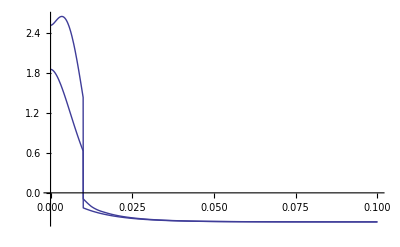

```mathematica
timetreat=60 60; (* Reset Treatment Time*)

Ebph=31.34*1000; (* cal/mol *)
Abph=6.2*10^17; (* 1/s *)
Etumor=135.7*1000; (* cal/mol *)
Atumor=1.7*10^91; (* 1/s *)
R=1.987; (* cal/mol-K *)

ΩCONS[dist_]:=NIntegrate[ If[dist≤rtumor,Atumor,Abph] Exp[-If[dist≤rtumor,Etumor,Ebph]/(R*(Evaluate[u[x,t]/.solutionCONfeo/.x->dist]+273.15))],{t,0,timetreat*2},MaxRecursion->100];
ΩCONS[rtumor]
ΩEXP[dist_]:=NIntegrate[ If[dist≤rtumor,Atumor,Abph] Exp[-If[dist≤rtumor,Etumor,Ebph]/(R*(Evaluate[u[x,t]/.solutionEXPfeo/.x->dist]+273.15))],{t,0,timetreat*2},MaxRecursion->100];
ΩEXP[rtumor]

PlotΩCONS=Plot[Log[10,ΩCONS[x]],{x,10^-20,rtissue},(*PlotPoints->20,*)PlotRange->All];
PlotΩEXP=Plot[Log[10,ΩEXP[x]],{x,10^-20,rtissue},(*PlotPoints->20,*)PlotRange->All];

Show[PlotΩCONS,PlotΩEXP]
```